# Support Vector Machines

## Demonstrace funkce a použití SVM klasifikátoru

bla bla upravit jmena promennzch v manipulatech

```mathematica
SetDirectory[NotebookDirectory[]];
Quiet[<<MathSVM`];
Needs["VectorAnalysis`"];
```

```mathematica
SVMPlotMy[α_,X_?MatrixQ,y_,opts___]:=Module[{x1range,x2range,sv,df,x1,x2,K},K=KernelFunction/.{opts}/.Options[SVMPlot];
x1range={x1,Min[X[[All,1]]],Max[X[[All,1]]]};
x2range={x2,Min[X[[All,2]]],Max[X[[All,2]]]};
sv=SupportVectors[α,y];
df=Total[α*y*Map[K[{x1,x2},#]&,X]]+Bias[α,X,y,opts];
Show[ListPlot[X[[Flatten[sv]]],PlotStyle->{Hue[0.6],PointSize[0.020]}],ListPlot[Extract[X,Position[y,1]],PlotStyle->{Red}],ListPlot[Extract[X,Position[y,-1]],PlotStyle->{Green}],ImplicitPlot[df==0,x1range,x2range,PlotStyle->{Thick}],ImplicitPlot[df==1,x1range,x2range,PlotStyle->Dashing[{.01,.01}]],ImplicitPlot[df==-1,x1range,x2range,PlotStyle->Dashing[{.01,.01}]],PlotRange->All(*,RemainingOptions[{KernelFunction},opts]*)]];
KernelRBF[x_,z_, b_]:=Exp[-b (x-z) (x-z)];
KernelPolynomial[x_,z_,c_,d_Integer]:=(c+x z)^d;
```

```mathematica
points=20;
x=Join[RandomReal[NormalDistribution[-2,1],{points/2,2}],
RandomReal[NormalDistribution[2,1],{points/2,2}]];
y=Join[Table[1,{points/2}],Table[-1,{points/2}]];
```

```mathematica
ListPlot[{Extract[x,Position[y,1]],Extract[x,Position[y,-1]]},PlotStyle->{Red,Green}, PlotRange->All]
```

```mathematica
t=0.01;
a=SeparableSVM[x,y,t]
```

```mathematica
SVMPlotMy[a,x,y]
```

```mathematica
Manipulate[ab1=SeparableSVM[x,y,t];
SVMPlotMy[ab1,x,y],{t,0.00001,0.5},ContinuousAction->False]
```

```mathematica
points2=50;
xx=Join[RandomReal[NormalDistribution[-3,2],{points2/2,2}],
RandomReal[NormalDistribution[2,3],{points2/2,2}]];
yy=Join[Table[1,{points2/2}],Table[-1,{points2/2}]];
ListPlot[{Extract[xx,Position[yy,1]],Extract[xx,Position[yy,-1]]},PlotStyle->{Red,Green}, PlotRange->All]
```

```mathematica
aa=NonseparableSVM[xx,yy,0.5,0.01];
SVMPlotMy[aa,xx,yy]
```

```mathematica
Manipulate[ab=NonseparableSVM[xx,yy,e,0.01];
SVMPlotMy[ab,xx,yy],{e,0.001,3},ContinuousAction->False]
```

## Polynomial kernel

```mathematica
Manipulate[Plot3D[KernelPolynomial[x,z,1,d],{x,-4,4},{z,-4,4},ViewPoint->{-7.654,-1.091,4.608},PlotPoints->{30,30}],{{d,1,"Stupen polynomu"},1,20,1}]
```

```mathematica
Manipulate[pk=PolynomialKernel[#1,#2,t]&;
aab=NonseparableSVM[xx,yy,0.5,0.01, KernelFunction->pk];
SVMPlotMy[aab,xx,yy,KernelFunction->pk],{{t,1,"Stupen polynomu"},1,10,1},ContinuousAction->False]
```

## RBF kernel

```mathematica
Manipulate[Plot3D[KernelRBF[x,z,t],{x,-10,10},{z,-10,10},ViewPoint->{3.849,6.909,4.295},PlotPoints->{30,30}],{{t,0.000001,"Rozptyl"},0.000001,0.5}]
```

```mathematica
Manipulate[RBFk=RBFKernel[#1,#2,t]&;
aaa=NonseparableSVM[xx,yy,e,0.01, KernelFunction->RBFk];
SVMPlotMy[aaa,xx,yy,KernelFunction->RBFk],{{t,0.02,"strmost fce"},0.0001,3,0.01},{{e,0.5,"Vyznam chyby"},0.0001,10},ContinuousAction->False]
```

Stupen polynomu a hodnota strmosti RBF se zjistuji experimentalne...nejcasteji krizovou validaci.

## Identity kernel

== žádný kernel

```mathematica
KernelIdentity[x_,z_] := x*z;
Plot3D[KernelIdentity[x,z],{x,0,10},{z,-10,10},PlotPoints->{30,30}]
```

## Ilustrace prechodu do vyssi dimenze

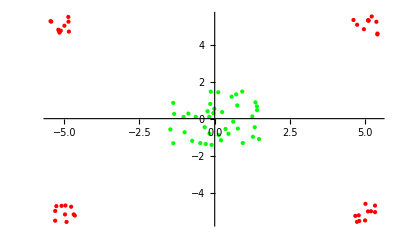

```mathematica
values = 40;
inRing=Join[ Join[RandomReal[{-5.5,-4.6},{values/4,1}],
RandomReal[{-5.6,-4.5},{values/4,1}],2],
Join[RandomReal[{5.5,4.6},{values/4,1}],
RandomReal[{5.6,4.5},{values/4,1}],2],
Join[RandomReal[{-5.5,-4.6},{values/4,1}],
RandomReal[{5.6,4.5},{values/4,1}],2],
Join[RandomReal[{5.5,4.6},{values/4,1}],
RandomReal[{-5.6,-4.5},{values/4,1}],2]];
inCentral =Join[RandomReal[{-1.5,1.5},{values,1}],
RandomReal[{-1.5,1.5},{values,1}],2];
inputData = Join[inRing,inCentral];
inputClasses=Join[Table[1,{values}],Table[-1,{values}]];
ListPlot[{Extract[inputData,Position[inputClasses,1]],Extract[inputData,Position[inputClasses,-1]]},PlotStyle->{Red,Green}, PlotRange->All]
```

```mathematica
polynomDegree = 4;
RBFparam = 0.1;
KRBF= RBFKernel[#1,#2,RBFparam]&;
KPol=PolynomialKernel[#1,#2,polynomDegree]&;
```

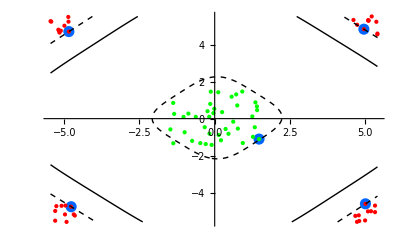

```mathematica
gg=SeparableSVM[inputData,inputClasses,0.01,KernelFunction->KPol];
SVMPlotMy[gg,inputData,inputClasses,KernelFunction->KPol]
```

```mathematica
KernelPolynomialSpec[x_]:={x[[1]],x[[2]],(1+x[[1]] x[[2]])^polynomDegree};
KernelRBFSpec[x_]:={x[[1]],x[[2]], Exp[-RBFparam (x[[1]]-x[[2]]) (x[[1]]-x[[2]])]};
```

```mathematica
higherDim = KernelPolynomialSpec/@inputData;
Show[ListPointPlot3D[{Extract[higherDim,Position[inputClasses,1]],Extract[higherDim,Position[inputClasses,-1]]},PlotStyle->{{Red,PointSize[Medium]},{Green,PointSize[Medium]}},PlotRange->All],
Plot3D[KernelPolynomial[x,z,1,polynomDegree],{x,-5.5,5.5},{z,-5.5,5.5},PlotPoints->{30,30},PlotRange->All,PlotStyle->Opacity[0.3],Mesh->None]]
```

-Graphics3D-

```mathematica
vectors=Take[Sort[Join[Take[Sort[Extract[higherDim,Position[inputClasses,1]][[;;values/4]],#1[[3]]<#2[[3]]&],1],Take[Sort[Extract[higherDim,Position[inputClasses,1]][[values/4;;values/2]],#1[[3]]<#2[[3]]&],1],Take[Sort[Extract[higherDim,Position[inputClasses,1]][[values/2;;3*values/4]],#1[[3]]<#2[[3]]&],1],Take[Sort[Extract[higherDim,Position[inputClasses,1]][[3*values/4;;values]],#1[[3]]<#2[[3]]&],1]],#1[[3]]<#2[[3]]&],3];
vectors2=Sort[Join[Take[Sort[Extract[higherDim,Position[inputClasses,-1]],#1[[3]]<#2[[3]]&],1]]];
v1=vectors[[1]]-vectors[[2]];
v2=vectors[[3]]-vectors[[2]];
normal=CrossProduct[v1,v2];
aa=normal[[3]];
d=Dot[normal,vectors[[1]]];
formula=normal*{x,y,1};
formula = Plus@@formula;
formula=(formula-d)/-aa;
dd=Dot[normal,vectors2[[1]]];
formula2=normal*{x,y,1};
formula2 = Plus@@formula2;
formula2=(formula2-dd)/-aa;
F[x_,y_]:=(Total[normal*{x,y,1}]-d)/-aa;
F2[x_,y_]:=(Total[normal*{x,y,1}]-dd)/-aa;
```

```mathematica
formula3=normal*{x,y,1};
formula3 = Plus@@formula3;
ddd=Dot[normal,{0,0,Abs[F[0,0]-F2[0,0]]/2}];
formula3=((formula3-ddd)/-aa);
F3[x_,y_]:=(Total[normal*{x,y,1}]-ddd)/-aa;
Show[ListPointPlot3D[{Extract[higherDim,Position[inputClasses,1]],Extract[higherDim,Position[inputClasses,-1]]},PlotStyle->{{Red,PointSize[Medium]},{Green,PointSize[Medium]}},PlotRange->All],
 Plot3D[formula,{x,-5.5,5.5},{y,-5.5,5.5},Mesh->None,PlotStyle->Opacity[0.2]],
Plot3D[formula2,{x,-5.5,5.5},{y,-5.5,5.5},Mesh->None,PlotStyle->Opacity[0.2]],
Plot3D[formula3,{x,-5.5,5.5},{y,-5.5,5.5},Mesh->None,PlotStyle->Opacity[0.4]],ListPointPlot3D[vectors[[;;3]], PlotStyle->{PointSize[0.020],Hue[0.6]}],ListPointPlot3D[vectors2[[;;1]], PlotStyle->{PointSize[0.020],Hue[0.6]}],ViewPoint->{15,6,4}]
```

-Graphics3D-

```mathematica
range=10;
Show[Plot3D[KernelPolynomial[x,z,1,polynomDegree],{x,-range,range},{z,-range,range},PlotRange->All,PlotStyle->Opacity[0],Mesh->None,RegionFunction->Function[{x,y,z},z>F[x,y]],BoundaryStyle->{Dashing[{.001,.001}]}],Plot3D[KernelPolynomial[x,z,1,polynomDegree],{x,-range,range},{z,-range,range},PlotRange->All,PlotStyle->Opacity[0],Mesh->None,RegionFunction->Function[{x,y,z},z>F2[x,y]],BoundaryStyle->{Dashing[{.001,.001}]}],Plot3D[KernelPolynomial[x,z,1,polynomDegree],{x,-range,range},{z,-range,range},PlotRange->All,PlotStyle->Opacity[0],Mesh->None,RegionFunction->Function[{x,y,z},z>F3[x,y]],BoundaryStyle->{Thick}],ListPointPlot3D[{Extract[higherDim,Position[inputClasses,1]],Extract[higherDim,Position[inputClasses,-1]]},PlotStyle->{{Red,PointSize[Medium]},{Green,PointSize[Medium]}},PlotRange->All],ListPointPlot3D[vectors[[;;3]],PlotStyle->Directive[PointSize[Large],Opacity[0.5]]],ListPointPlot3D[vectors2[[;;1]],PlotStyle->Directive[PointSize[Large],Opacity[0.5]]],ViewPoint->{0,0,10}]
```

-Graphics3D-

## Iris data

použití svm na realnych datech

SVM v zakladni podobe umi pouze klafifikovat do dvou trid. proto je treba ho zobecnit.
Pro multiclass problem je vice moznosti, jak zobecnit. my pouzijeme nejsnazsi a to ze rozdelime data na jednu tridu a ostatni a ty klasifikujeme. tohle deleni se udela pro vsechny tridy. vysledna klasifikace se urci jako majorita z dilcich klasifikatoru.

```mathematica
data=Import["http://ftp.ics.uci.edu/pub/machine-learning-databases/iris/iris.data"];
```

```mathematica
data2=Drop[data,-1];
inData=data2[[All,1;;4]];(*vstupní parametry*)
outDataTmp=data2[[All,5]];(*výstupní parametr*)outVal=Tally[outDataTmp][[All,1]];
encode=MapIndexed[#1->Normal[#2]&,outVal];
outData=Flatten[Flatten[outDataTmp]/.encode];
Func[x_,y_]:= If[y==x,1,-1];
outDataC1=Map[Func[#,1]&,outData];
outDataC2=Map[Func[#,2]&,outData];
outDataC3=Map[Func[#,3]&,outData];
```

```mathematica
PolDegree=10;
RBFparam = 0.001;
error=0.8;
precision=0.01;
PolKer = PolynomialKernel[#1,#2,PolDegree]&;
RBFKer=RBFKernel[#1,#2,RBFparam]&;
```

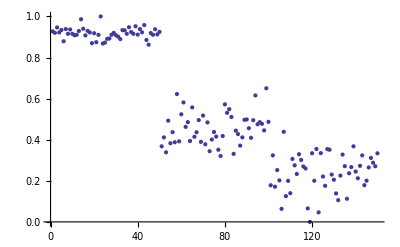

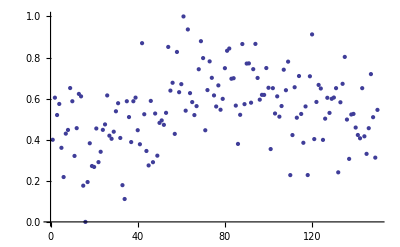

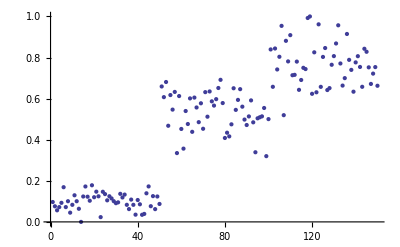

```mathematica
l=NonseparableSVM[inData,outDataC1,error,precision,KernelFunction->RBFKer];
out1=Rescale[inData.WeightVector[l,inData,outDataC1]];
ListPlot[out1]
ll=NonseparableSVM[inData,outDataC2,error,precision,KernelFunction->RBFKer];
out2=Rescale[inData.WeightVector[ll,inData,outDataC2]];
ListPlot[out2]
lll=NonseparableSVM[inData,outDataC3,error,precision, KernelFunction->RBFKer];
out3=Rescale[inData.WeightVector[lll,inData,outDataC3]];
ListPlot[out3]
```

Znormalizovany je to aby slo porovnavat relativni velikost vystupu. Ten, ktery da nejvyssi vystup, ten vyhrava a lepi svou cedulku.

```mathematica
MyCompare[a_,b_,c_]:=If[a>=b&&a≥c,1,If[b≥a&&b≥c,2,3]];
MyCorrect[a_,b_]:=If[a==b,1,0];
```

```mathematica
out={};
For[i=1,i≤Dimensions[out3][[1]],i++,
AppendTo[out,MyCompare[out1[[i]],out2[[i]],out3[[i]]]]
];
```

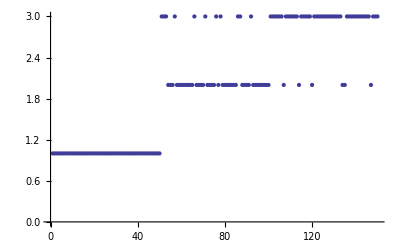

```mathematica
ListPlot[out]
```

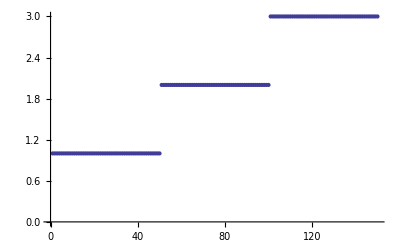

```mathematica
ListPlot[outData]
```

Úspěšnost klasifikace

```mathematica
correct=0;
 For[i=1,i≤Dimensions[out3][[1]],i++,
correct+=MyCorrect[out[[i]],outData[[i]]];
];
N[correct/Dimensions[outData][[1]]*100,5]
```

88.667